```mathematica
Get[FileNameJoin[{NotebookDirectory[], "functions.m"}]]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"];
b2 = MergeDirections["2_Ashwood_RGU.txt", "2_RGU_Ashwood.txt"];
b3 = MergeDirections["3_Cove_Mastrick.txt", "3_Mastrick_Cove.txt"];
b11 = MergeDirections["11_Northfield_Woodend.txt", "11_Woodend_Northfield.txt"];
b12 = MergeDirections["12_Heathryfold_Torry.txt", "12_Torry_Heathryfold.txt"];
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"];
b15 = MergeDirections["15_Balnagask_Circle_Countesswells.txt", "15_Countesswells_Balnagask_Circle.txt"];
b17 = MergeDirections["17_Dyce_Faulds_Gate.txt", "17_Faulds_Gate_Dyce.txt"];
b18 = MergeDirections["18_Dyce_Redmoss.txt", "18_Redmoss_Dyce.txt"];
b19 = MergeDirections["19_Culter_Tillydrone.txt", "19_Tillydrone_Culter.txt"];
b20 = MergeDirections["20_Guild_str_Hillhead.txt", "20_Hillhead_Guild_str.txt"];
b23 = MergeDirections["23_Raasay_Gardens_Heathryfold.txt",  "23_Heathryfold_Raasay_Gardens.txt"];
```

```mathematica
buses = {b1, b3, b11, b12, b13, b15, b17, b18, b19, b20, b23};
routeNames = {"1", "3", "11", "12", "13", "15", "17", "18", "19", "20", "23"};
```

```mathematica
TAPs=Algorithm821[buses, routeNames, Quantity[15, "Minutes"]];
```

```mathematica
Max[#[[2]]&/@Values[TAPs[[3]]]]
```

1

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

```mathematica
Dimensions[mtx]
```

{122,122}

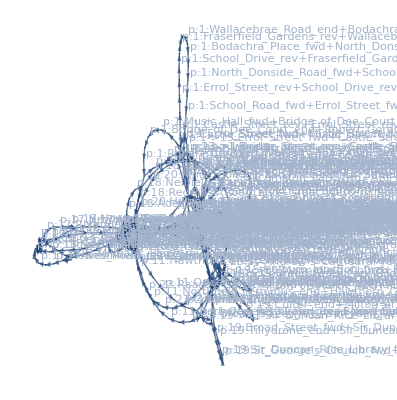

```mathematica
CreatePetriNetFromTAPs[TAPs]
```

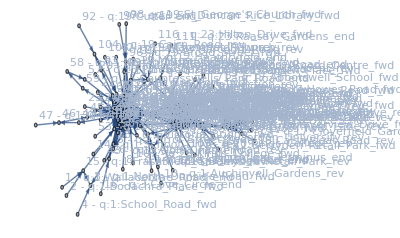

```mathematica
MakeAdjacencyGraph[mtx, TAPs]
```

```mathematica
v = MakeStateVector[mtx]
```

{-∞,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,-∞,0,0,-∞,0,-∞,0,0,-∞,0,0,-∞,-∞,0,-∞,0,0,0,-∞,-∞,0,0,0,-∞,0,0,0,-∞,0,-∞,0,-∞,0,0,0,0,0,-∞,0,-∞,-∞,0,-∞,0,0,-∞,0,-∞,0,0,-∞,-∞,0,-∞,0,-∞,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,0,0,-∞,-∞,0,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,0,0,-∞,0,-∞,0}

```mathematica
ttb = TimeTable[mtx,v, TAPs[[1]]];
```

```mathematica
ttb // Transpose // MatrixForm
```

(q:1:Wallacebrae_Road_end | -∞ | 13. | 25. | 67. | 97.
q:1:Bodachra_Place_fwd | -∞ | 20. | 32. | 74. | 104.
q:1:North_Donside_Road_fwd | 0 | 27. | 39. | 81. | 111.
q:1:School_Road_fwd | -∞ | 7. | 34. | 46. | 88.
q:1:Errol_Street_fwd | 0 | 12. | 39. | 51. | 93.
q:1:Castle_Street_fwd | -∞ | 38. | 68. | 102. | 132.
q:1:Music_Hall_fwd | 0 | 43. | 73. | 107. | 137.
q:1:Bridge_of_Dee_Court_end | -∞ | 14. | 57. | 87. | 121.
q:1:Robert_Gordon_University_rev | 0 | 18. | 61. | 91. | 125.
q:1:Auchinyell_Gardens_rev | -∞ | 8. | 26. | 69. | 99.
q:1:Great_Western_Road_rev | 0 | 23. | 34. | 77. | 107.
q:1:Castle_Street_rev | -∞ | 38. | 68. | 102. | 132.
q:1:Errol_Street_rev | 0 | 42. | 72. | 106. | 136.
q:1:School_Drive_rev | -∞ | 5. | 47. | 77. | 111.
q:1:Fraserfield_Gardens_rev | 0 | 12. | 54. | 84. | 118.
q:3:Cove_Circle_end | -∞ | 9. | 18. | 50. | 70.
q:3:Altens_Farm_Road_fwd | 0 | 19. | 28. | 60. | 80.
q:3:Victoria_Bridge_fwd | -∞ | 25. | 57. | 87. | 121.
q:3:Guild_Street_fwd | 0 | 32. | 62. | 96. | 126.
q:3:Gilcomston_Park_fwd | -∞ | 6. | 38. | 68. | 102.
q:3:ARI_Bus_Port_fwd | 0 | 17. | 49. | 79. | 113.
q:3:Mastrick_end | 0 | 10. | 27. | 59. | 89.
q:3:Aberdeen_Royal_Infirmary_rev | -∞ | 9. | 19. | 36. | 68.
q:3:Bridge_Street_rev | -∞ | 19. | 46. | 78. | 108.
q:3:Guild_Street_rev | 0 | 32. | 52. | 96. | 126.
q:3:Altens_Farm_Road_rev | 0 | 9. | 41. | 61. | 105.
q:11:Northfield_Terminus_end | -∞ | 23. | 38. | 73. | 105.
q:11:Hawthorn_Crescent_fwd | 0 | 31. | 46. | 81. | 113.
q:11:Berryden_Retail_Park_fwd | -∞ | 9. | 40. | 55. | 90.
q:11:Adelphi_fwd | 0 | 21. | 51. | 76. | 106.
q:11:Queen's_Cross_fwd | 0 | 12. | 33. | 63. | 88.
q:11:Woodend_end | -∞ | 8. | 20. | 41. | 71.
q:11:Queen's_Cross_rev | 0 | 16. | 28. | 49. | 79.
q:11:Broad_Street_rev | 0 | 15. | 50. | 82. | 112.
q:11:Berryden_Retail_Park_rev | -∞ | 11. | 26. | 61. | 93.
q:12:Heathryfold_end | -∞ | 24. | 56. | 86. | 120.
q:12:Belmont_Road_fwd | 0 | 36. | 68. | 98. | 132.
q:12:Bridge_Street_fwd | -∞ | 19. | 46. | 78. | 108.
q:12:Guild_Street_fwd | 0 | 32. | 62. | 96. | 126.
q:12:Torry_Terminus_end | 0 | 10. | 42. | 72. | 106.
q:12:Guild_Street_rev | 0 | 32. | 62. | 96. | 126.
q:12:Chestnut_Row_rev | -∞ | 14. | 46. | 76. | 110.
q:13:Golf_Links_end | -∞ | 14. | 58. | 88. | 122.
q:13:Beach_Boulevard_fwd | 0 | 24. | 68. | 98. | 132.
q:13:St_Andrew's_Cathedral_fwd | 0 | 14. | 34. | 78. | 108.
q:13:Prince_Arthur_Street_fwd | 0 | 13. | 27. | 47. | 91.
q:13:Mastrick_Shops_fwd | -∞ | 15. | 28. | 42. | 62.
q:13:Turning_Circle_end | 0 | 24. | 37. | 51. | 71.
q:13:Summerhill_Terrace_rev | 0 | 15. | 39. | 52. | 66.
q:13:Bridge_Street_rev | 0 | 19. | 46. | 78. | 108.
q:13:Castle_Street_rev | -∞ | 38. | 68. | 102. | 132.
q:13:Beach_Boulevard_rev | 0 | 44. | 74. | 108. | 138.
q:15:Balnagask_Circle_end | -∞ | 14. | 46. | 76. | 110.
q:15:Victoria_Bridge_fwd | 0 | 25. | 57. | 87. | 121.
q:15:Guild_Street_fwd | -∞ | 30. | 62. | 92. | 126.
q:15:Holburn_Junction_fwd | 0 | 41. | 73. | 103. | 137.
q:15:Pinewood_Place_fwd | 0 | 15. | 56. | 88. | 118.
q:15:North_Countesswells_Road_fwd | 0 | 15. | 30. | 71. | 103.
q:15:Countesswells_Park_Road_end | 0 | 6. | 21. | 36. | 77.
q:15:Airyhall_rev | 0 | 15. | 21. | 36. | 51.
q:15:Holburn_Junction_rev | -∞ | 23. | 43. | 87. | 117.
q:15:Guild_Street_rev | 0 | 32. | 62. | 96. | 126.
q:17:Dyce_end | -∞ | 17. | 39. | 60. | 90.
q:17:Riverview_Drive_fwd | -∞ | 28. | 50. | 71. | 101.
q:17:Newhills_fwd | 0 | 36. | 58. | 79. | 109.
q:17:Howes_Road_fwd | -∞ | 10. | 46. | 68. | 89.
q:17:Mugiemoss_Road_fwd | 0 | 17. | 53. | 75. | 96.
q:17:Millbank_Place_fwd | 0 | 10. | 27. | 63. | 85.
q:17:Bon_Accord_Centre_fwd | -∞ | 6. | 16. | 33. | 69.
q:17:Adelphi_fwd | 0 | 21. | 51. | 76. | 106.
q:17:Abbotswell_School_fwd | -∞ | 13. | 34. | 64. | 89.
q:17:Faulds_Gate_end | 0 | 19. | 40. | 70. | 95.
q:17:Devanha_Gardens_rev | 0 | 11. | 30. | 51. | 81.
q:17:Adelphi_rev | -∞ | 21. | 51. | 76. | 106.
q:17:Bon_Accord_Centre_rev | -∞ | 25. | 55. | 80. | 110.
q:17:Millbank_Place_rev | 0 | 29. | 59. | 84. | 114.
q:17:Smithfield_Lane_rev | -∞ | 16. | 37. | 67. | 92.
q:17:Howes_Road_rev | 0 | 22. | 43. | 73. | 98.
q:17:Cloverfield_Gardens_rev | -∞ | 8. | 30. | 51. | 81.
q:18:Dyce_end | -∞ | 17. | 39. | 60. | 90.
q:18:Riverview_Drive_fwd | 0 | 28. | 50. | 71. | 101.
q:18:Mugiemoss_Road_fwd | 0 | 17. | 53. | 75. | 96.
q:18:Powis_Lane_fwd | -∞ | 10. | 27. | 63. | 85.
q:18:Adelphi_fwd | 0 | 21. | 51. | 76. | 106.
q:18:Nellfield_Place_fwd | 0 | 10. | 31. | 61. | 86.
q:18:Redmoss_Road_end | -∞ | 11. | 21. | 42. | 72.
q:18:Great_Western_Road_rev | 0 | 23. | 34. | 77. | 107.
q:18:Adelphi_rev | 0 | 21. | 51. | 76. | 106.
q:18:Calsayseat_Road_rev | -∞ | 7. | 28. | 58. | 83.
q:18:Smithfield_Lane_rev | 0 | 16. | 37. | 67. | 92.
q:18:Riverview_Drive_rev | 0 | 21. | 43. | 64. | 94.
q:19:Culter_end | -∞ | 13. | 35. | 76. | 108.
q:19:Milton_of_Murtle_fwd | 0 | 27. | 49. | 90. | 122.
q:19:Mannofield_Church_fwd | 0 | 15. | 42. | 64. | 105.
q:19:Holburn_Junction_fwd | 0 | 41. | 73. | 103. | 137.
q:19:Broad_Street_fwd | 0 | 10. | 50. | 82. | 112.
q:19:Sir_Duncan_Rice_Library_fwd | -∞ | 14. | 24. | 64. | 96.
q:19:St_George's_Church_fwd | -∞ | 17. | 27. | 67. | 99.
q:19:Tillydrone_end | 0 | 20. | 30. | 70. | 102.
q:19:Sir_Duncan_Rice_Library_rev | 0 | 8. | 28. | 38. | 78.
q:19:Broad_Street_rev | -∞ | 15. | 26. | 43. | 59.
q:19:Holburn_Junction_rev | 0 | 41. | 73. | 103. | 137.
q:19:Mannofield_Church_rev | -∞ | 11. | 52. | 84. | 114.
q:19:Cairn_Road_rev | 0 | 22. | 63. | 95. | 125.
q:20:Guild_Street_end | -∞ | 32. | 62. | 96. | 126.
q:20:Castle_Street_fwd | 0 | 38. | 68. | 102. | 132.
q:20:Kings_College_fwd | -∞ | 9. | 47. | 77. | 111.
q:20:Hillhead_Of_Seaton_end | 0 | 17. | 55. | 85. | 119.
q:20:Kings_College_rev | -∞ | 9. | 26. | 64. | 94.
q:20:Adelphi_rev | 0 | 21. | 51. | 76. | 106.
q:23:Raasay_Gardens_end | -∞ | 4. | 21. | 62. | 94.
q:23:Raeden_Avenue_fwd | 0 | 14. | 31. | 72. | 104.
q:23:Carden_Place_fwd | -∞ | 9. | 23. | 40. | 81.
q:23:Adelphi_fwd | 0 | 21. | 51. | 76. | 106.
q:23:Fraser_Place_fwd | 0 | 7. | 28. | 58. | 83.
q:23:Hilton_Drive_fwd | -∞ | 9. | 16. | 37. | 67.
q:23:Heathryfold_end | 0 | 24. | 56. | 86. | 120.
q:23:Hilton_Drive_rev | 0 | 11. | 35. | 67. | 97.
q:23:St_Andrew's_Cathedral_rev | -∞ | 14. | 34. | 78. | 108.
q:23:Holburn_Junction_rev | 0 | 41. | 73. | 103. | 137.
q:23:Harcourt_Road_rev | -∞ | 9. | 50. | 82. | 112.
q:23:Colonsay_Crescent_rev | 0 | 17. | 58. | 90. | 120.)

```mathematica
ExportMaxPlusMatrix["matrix_ct15", mtx]
```

```mathematica
routes = SplitByRoutes[ttb, routeNames];
```

```mathematica
ConvertToHoursTimetable[routes[[1]]] // MatrixForm
```

(q:1:Wallacebrae_Road_end | 06:13:00GMT+1TimeObject[{6,13,0},Instant,1.] | 06:25:00GMT+1TimeObject[{6,25,0},Instant,1.] | 07:07:00GMT+1TimeObject[{7,7,0},Instant,1.] | 07:37:00GMT+1TimeObject[{7,37,0},Instant,1.] | -
q:1:Bodachra_Place_fwd | 06:20:00GMT+1TimeObject[{6,20,0},Instant,1.] | 06:32:00GMT+1TimeObject[{6,32,0},Instant,1.] | 07:14:00GMT+1TimeObject[{7,14,0},Instant,1.] | 07:44:00GMT+1TimeObject[{7,44,0},Instant,1.] | -
q:1:North_Donside_Road_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:27:00GMT+1TimeObject[{6,27,0},Instant,1.] | 06:39:00GMT+1TimeObject[{6,39,0},Instant,1.] | 07:21:00GMT+1TimeObject[{7,21,0},Instant,1.] | 07:51:00GMT+1TimeObject[{7,51,0},Instant,1.]
q:1:School_Road_fwd | 06:07:00GMT+1TimeObject[{6,7,0},Instant,1.] | 06:34:00GMT+1TimeObject[{6,34,0},Instant,1.] | 06:46:00GMT+1TimeObject[{6,46,0},Instant,1.] | 07:28:00GMT+1TimeObject[{7,28,0},Instant,1.] | -
q:1:Errol_Street_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:12:00GMT+1TimeObject[{6,12,0},Instant,1.] | 06:39:00GMT+1TimeObject[{6,39,0},Instant,1.] | 06:51:00GMT+1TimeObject[{6,51,0},Instant,1.] | 07:33:00GMT+1TimeObject[{7,33,0},Instant,1.]
q:1:Castle_Street_fwd | 06:38:00GMT+1TimeObject[{6,38,0},Instant,1.] | 07:08:00GMT+1TimeObject[{7,8,0},Instant,1.] | 07:42:00GMT+1TimeObject[{7,42,0},Instant,1.] | 08:12:00GMT+1TimeObject[{8,12,0},Instant,1.] | -
q:1:Music_Hall_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:43:00GMT+1TimeObject[{6,43,0},Instant,1.] | 07:13:00GMT+1TimeObject[{7,13,0},Instant,1.] | 07:47:00GMT+1TimeObject[{7,47,0},Instant,1.] | 08:17:00GMT+1TimeObject[{8,17,0},Instant,1.]
q:1:Bridge_of_Dee_Court_end | 06:14:00GMT+1TimeObject[{6,14,0},Instant,1.] | 06:57:00GMT+1TimeObject[{6,57,0},Instant,1.] | 07:27:00GMT+1TimeObject[{7,27,0},Instant,1.] | 08:01:00GMT+1TimeObject[{8,1,0},Instant,1.] | -
q:1:Robert_Gordon_University_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:18:00GMT+1TimeObject[{6,18,0},Instant,1.] | 07:01:00GMT+1TimeObject[{7,1,0},Instant,1.] | 07:31:00GMT+1TimeObject[{7,31,0},Instant,1.] | 08:05:00GMT+1TimeObject[{8,5,0},Instant,1.]
q:1:Auchinyell_Gardens_rev | 06:08:00GMT+1TimeObject[{6,8,0},Instant,1.] | 06:26:00GMT+1TimeObject[{6,26,0},Instant,1.] | 07:09:00GMT+1TimeObject[{7,9,0},Instant,1.] | 07:39:00GMT+1TimeObject[{7,39,0},Instant,1.] | -
q:1:Great_Western_Road_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:23:00GMT+1TimeObject[{6,23,0},Instant,1.] | 06:34:00GMT+1TimeObject[{6,34,0},Instant,1.] | 07:17:00GMT+1TimeObject[{7,17,0},Instant,1.] | 07:47:00GMT+1TimeObject[{7,47,0},Instant,1.]
q:1:Castle_Street_rev | 06:38:00GMT+1TimeObject[{6,38,0},Instant,1.] | 07:08:00GMT+1TimeObject[{7,8,0},Instant,1.] | 07:42:00GMT+1TimeObject[{7,42,0},Instant,1.] | 08:12:00GMT+1TimeObject[{8,12,0},Instant,1.] | -
q:1:Errol_Street_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:42:00GMT+1TimeObject[{6,42,0},Instant,1.] | 07:12:00GMT+1TimeObject[{7,12,0},Instant,1.] | 07:46:00GMT+1TimeObject[{7,46,0},Instant,1.] | 08:16:00GMT+1TimeObject[{8,16,0},Instant,1.]
q:1:School_Drive_rev | 06:05:00GMT+1TimeObject[{6,5,0},Instant,1.] | 06:47:00GMT+1TimeObject[{6,47,0},Instant,1.] | 07:17:00GMT+1TimeObject[{7,17,0},Instant,1.] | 07:51:00GMT+1TimeObject[{7,51,0},Instant,1.] | -
q:1:Fraserfield_Gardens_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:12:00GMT+1TimeObject[{6,12,0},Instant,1.] | 06:54:00GMT+1TimeObject[{6,54,0},Instant,1.] | 07:24:00GMT+1TimeObject[{7,24,0},Instant,1.] | 07:58:00GMT+1TimeObject[{7,58,0},Instant,1.])